```mathematica
Table[{
With[{g= Graph[Table[With[{form=allGraphs6[k,"colofourrealnull"]},form-> Last[FactorTermsList[ DropMore[form,4,6]]]],{k,allGraphs6NullAtomKeys}],VertexLabels->"Name"]},
VertexInDegree[g,v]
],
v,
v/.repcolofourrealnullgraph2
},{v,realyNullAtomVars}]//Sort
```

{{5,n1234,-Graphics-n1234728},{10,n123x4,-Graphics-n123x4666},{10,n124x3,-Graphics-n124x3546},{10,n12x34,-Graphics-n12x34488},{10,n134x2,-Graphics-n134x2218},{10,n13x24,-Graphics-n13x24168},{10,n14x23,-Graphics-n14x2372},{10,n1x234,-Graphics-n1x23426},{17,n12x3x4,-Graphics-n12x3x4486},{17,n13x2x4,-Graphics-n13x2x4162},{17,n14x2x3,-Graphics-n14x2x354},{17,n1x23x4,-Graphics-n1x23x418},{17,n1x24x3,-Graphics-n1x24x36},{17,n1x2x34,-Graphics-n1x2x342},{26,n1x2x3x4,-Graphics-n1x2x3x40}}

```mathematica
Table[{
With[{g= Graph[Table[With[{form=allGraphs5[k,"colofourrealnull"]},form-> Last[FactorTermsList[ DropMore[form,4,5]]]],{k,allGraphs5NullAtomKeys}],VertexLabels->"Name"]},
VertexInDegree[g,v]
],
v,
v/.repcolofourrealnullgraph2
},{v,realyNullAtomVars}]//Sort
```

{{2,n1234,-Graphics-n1234728},{3,n123x4,-Graphics-n123x4666},{3,n124x3,-Graphics-n124x3546},{3,n12x34,-Graphics-n12x34488},{3,n134x2,-Graphics-n134x2218},{3,n13x24,-Graphics-n13x24168},{3,n14x23,-Graphics-n14x2372},{3,n1x234,-Graphics-n1x23426},{4,n12x3x4,-Graphics-n12x3x4486},{4,n13x2x4,-Graphics-n13x2x4162},{4,n14x2x3,-Graphics-n14x2x354},{4,n1x23x4,-Graphics-n1x23x418},{4,n1x24x3,-Graphics-n1x24x36},{4,n1x2x34,-Graphics-n1x2x342},{5,n1x2x3x4,-Graphics-n1x2x3x40}}

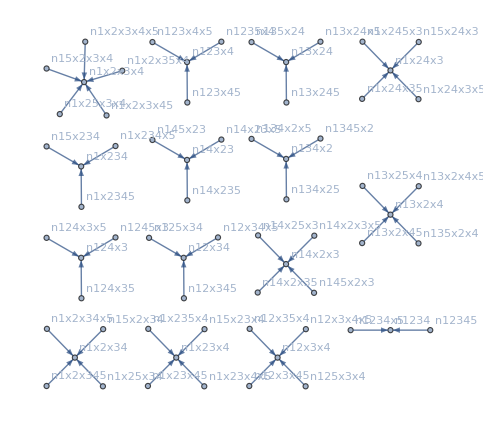

```mathematica
Graph[Table[With[{form=allGraphs5[k,"colofourrealnull"]},form-> Last[FactorTermsList[ DropMore[form,4,6]]]],{k,allGraphs5NullAtomKeys}],VertexLabels->"Name"]
```

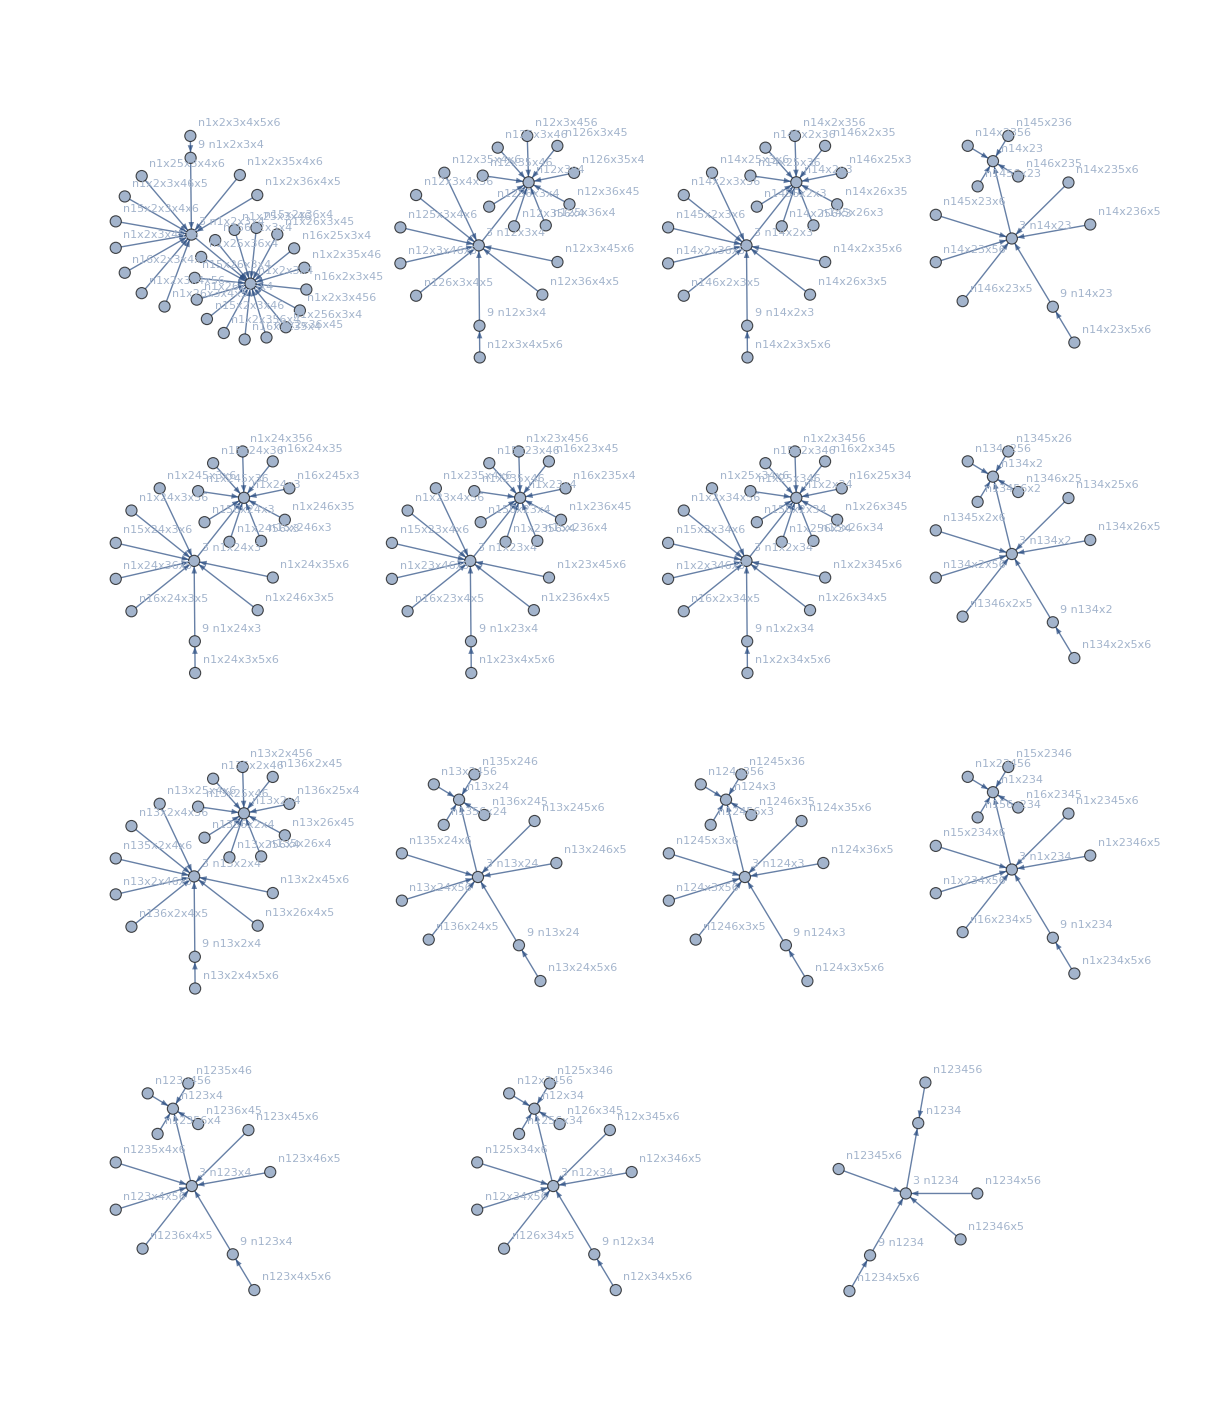

```mathematica
Block[
{result={},drop,rest,prefix},
Table[With[{form=allGraphs6[k,"colofourrealnull"]},
drop=DropMore[form,4,6];
result=Append[result,form-> drop];
{drop,rest}=FactorTermsList[drop];
While[drop>1,
result=Append[result,drop*rest-> (drop/3)*rest];
drop/=3
]
],{k,allGraphs6NullAtomKeys}]
;
result=DeleteDuplicates[result];
Graph[result,VertexLabels->"Name",GraphLayout->"BalloonEmbedding", ImageSize->Large]
]
```

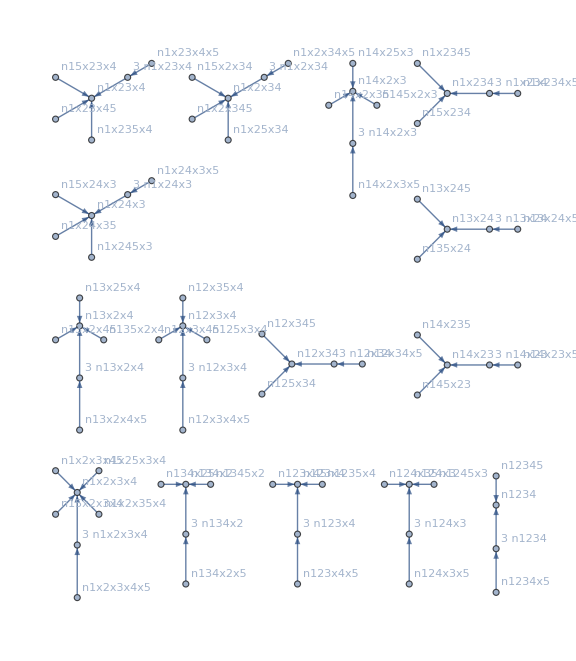

```mathematica
Block[
{result={},drop,rest,prefix},
Table[With[{form=allGraphs5[k,"colofourrealnull"]},
drop=DropMore[form,4,5];
result=Append[result,form-> drop];
{drop,rest}=FactorTermsList[drop];
While[drop>1,
result=Append[result,drop*rest-> (drop/3)*rest];
drop/=3
]
],{k,allGraphs5NullAtomKeys}]
;
result=DeleteDuplicates[result];
Graph[result,VertexLabels->"Name",GraphLayout->"BalloonEmbedding", ImageSize->Large]
]
```

```mathematica
joins=Table[allGraphs5[k,"colofourrealnull"]<->Last[FactorTermsList[ DropMore[allGraphs5[k,"colofourrealnull"],4,5]]],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5<->n1x2x3x4,n12x3x4x5<->n12x3x4,n123x4x5<->n123x4,n1234x5<->n1234,n12345<->n1234,n1235x4<->n123x4,n123x45<->n123x4,n124x3x5<->n124x3,n1245x3<->n124x3,n124x35<->n124x3,n125x3x4<->n12x3x4,n125x34<->n12x34,n12x34x5<->n12x34,n12x345<->n12x34,n12x35x4<->n12x3x4,n12x3x45<->n12x3x4,n13x2x4x5<->n13x2x4,n134x2x5<->n134x2,n1345x2<->n134x2,n134x25<->n134x2,n135x2x4<->n13x2x4,n135x24<->n13x24,n13x24x5<->n13x24,n13x245<->n13x24,n13x25x4<->n13x2x4,n13x2x45<->n13x2x4,n14x2x3x5<->n14x2x3,n145x2x3<->n14x2x3,n145x23<->n14x23,n14x23x5<->n14x23,n14x235<->n14x23,n14x25x3<->n14x2x3,n14x2x35<->n14x2x3,n15x2x3x4<->n1x2x3x4,n15x23x4<->n1x23x4,n15x234<->n1x234,n15x24x3<->n1x24x3,n15x2x34<->n1x2x34,n1x23x4x5<->n1x23x4,n1x234x5<->n1x234,n1x2345<->n1x234,n1x235x4<->n1x23x4,n1x23x45<->n1x23x4,n1x24x3x5<->n1x24x3,n1x245x3<->n1x24x3,n1x24x35<->n1x24x3,n1x25x3x4<->n1x2x3x4,n1x25x34<->n1x2x34,n1x2x34x5<->n1x2x34,n1x2x345<->n1x2x34,n1x2x35x4<->n1x2x3x4,n1x2x3x45<->n1x2x3x4}

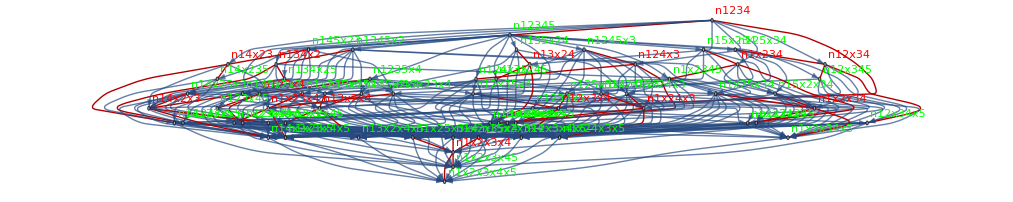

```mathematica
Graph[With[{g=GraphUnion[MobiusGraph3[K4Key,allGraphs],MobiusGraph3[k5Key,allGraphs5]]},
Graph[VertexList[g],Join[joins,EdgeList[g]]]],GraphHighlight->joins,VertexLabels->
Join[
Table[allGraphs5[k,"colofourrealnull"]->Style[allGraphs5[k,"colofourrealnull"],Green],{k,allGraphs5NullAtomKeys}],
Table[allGraphs[k,"colofourrealnull"]->Style[allGraphs[k,"colofourrealnull"],Red],{k,realyNullAtomKeys}]
],GraphLayout->"LayeredDigraphEmbedding"]
```

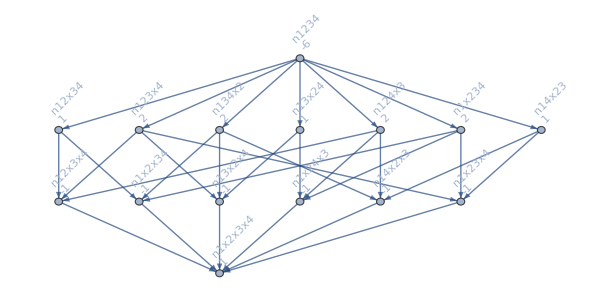

```mathematica
MobiusGraph3[K4Key,allGraphs]
```

```mathematica
Block[{allGraphs3},
allGraphs3=Get["d:\\Saved\\";
Graph[With[{g=GraphUnion[MobiusGraph3[K4Key,allGraphs],MobiusGraph3[k5Key,allGraphs5]]},
Graph[VertexList[g],Join[joins,EdgeList[g]]]],GraphHighlight->joins,VertexLabels->
Join[
Table[allGraphs5[k,"colofourrealnull"]->Style[allGraphs5[k,"colofourrealnull"],Green],{k,allGraphs5NullAtomKeys}],
Table[allGraphs[k,"colofourrealnull"]->Style[allGraphs[k,"colofourrealnull"],Yellow],{k,realyNullAtomKeys}]
],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
MobiusGraph3[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[from[[1]],to[[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
k3Key=First[Select[Keys[allGraphs3],IsomorphicGraphQ[allGraphs3[#,"graph"],CompleteGraph[3]]&]]
```

13

```mathematica
k2Key=First[Select[Keys[allGraphs2],IsomorphicGraphQ[allGraphs2[#,"graph"],CompleteGraph[2]]&]]
```

1

```mathematica
joins2=Table[DirectedEdge[allGraphs4[k,"colofourrealnull"],Last[FactorTermsList[ DropMore[allGraphs4[k,"colofourrealnull"],3]]]],{k,allGraphs4NullAtomKeys}]
```

{n1x2x3x4->n1x2x3,n12x3x4->n12x3,n123x4->n123,n1234->n123,n124x3->n12x3,n12x34->n12x3,n13x2x4->n13x2,n134x2->n13x2,n13x24->n13x2,n14x2x3->n1x2x3,n14x23->n1x23,n1x23x4->n1x23,n1x234->n1x23,n1x24x3->n1x2x3,n1x2x34->n1x2x3}

```mathematica
joinsLabels=Table[DirectedEdge[allGraphs4[k,"colofourrealnull"],Last[FactorTermsList[ DropMore[allGraphs4[k,"colofourrealnull"],3]]]]->Style[First[FactorTermsList[DropMore[allGraphs4[k,"colofourrealnull"],3]]],Bold,Blue,14],{k,allGraphs4NullAtomKeys}]
```

{n1x2x3x4->n1x2x3→2,n12x3x4->n12x3→2,n123x4->n123→2,n1234->n123→1,n124x3->n12x3→1,n12x34->n12x3→1,n13x2x4->n13x2→2,n134x2->n13x2→1,n13x24->n13x2→1,n14x2x3->n1x2x3→1,n14x23->n1x23→1,n1x23x4->n1x23→2,n1x234->n1x23→1,n1x24x3->n1x2x3→1,n1x2x34->n1x2x3→1}

```mathematica
joins3=Table[DirectedEdge[allGraphs3[k,"colofourrealnull"],Last[FactorTermsList[ DropMore[allGraphs3[k,"colofourrealnull"],2]]]],{k,allGraphs3NullAtomKeys}]
```

{n1x2x3->n1x2,n12x3->n12,n123->n12,n13x2->n1x2,n1x23->n1x2}

```mathematica
joins3Labels=Table[DirectedEdge[allGraphs3[k,"colofourrealnull"],Last[FactorTermsList[ DropMore[allGraphs3[k,"colofourrealnull"],2]]]]->Style[First[FactorTermsList[DropMore[allGraphs3[k,"colofourrealnull"],2]]],Bold,Blue,14],{k,allGraphs3NullAtomKeys}]
```

{n1x2x3->n1x2→1,n12x3->n12→1,n123->n12→1,n13x2->n1x2→1,n1x23->n1x2→1}

```mathematica
joins3Labels=Table[DirectedEdge[allGraphs3[k,"colofourrealnull"],Last[FactorTermsList[ DropMore[allGraphs3[k,"colofourrealnull"],2]]]]->Style[First[FactorTermsList[DropMore[allGraphs3[k,"colofourrealnull"],2]]],Bold,Blue,14],{k,allGraphs3NullAtomKeys}]
```

{n1x2x3->n1x2→1,n12x3->n12→1,n123->n12→1,n13x2->n1x2→1,n1x23->n1x2→1}

```mathematica
allGraphs4[K4Key]
```

<|signature→364,matrix→{{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4}},vertices→{1,2,3,4},edges→{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4},relations→{x364==x363-x365,x364==x361-x367,x364==x355-x373,x364==x337-x391,x364==x283-x445,x364==x121-x607},links→{},parents→{363,361,355,337,283,121},children→{},comp→GreaterEqual,compwhy→No IH,colofour→v1x2x3x4,colortable→{{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4},{0,v1x2x3x4}},colofournull→p1234,colofourrealnull→-6 n1234+2 n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4|>

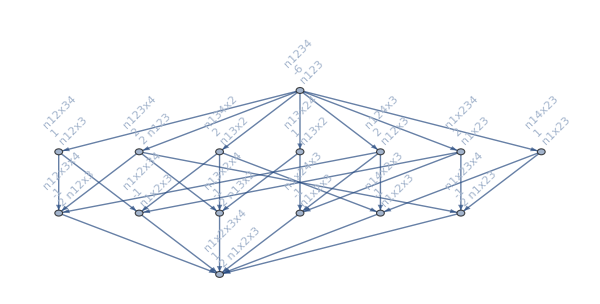

```mathematica
MobiusGraph4[K4Key,allGraphs4]
```

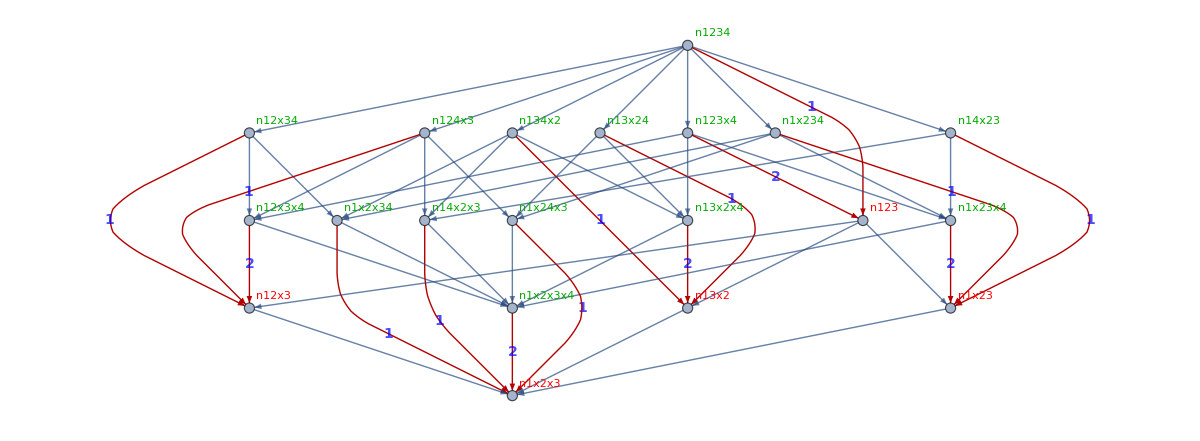

```mathematica
Graph[With[{g=MobiusGraph3[K4Key,allGraphs4],h=MobiusGraph3[k3Key,allGraphs3]},
Graph[Join[VertexList[g],VertexList[h]],Join[joins2,EdgeList[g],EdgeList[h]]]],
GraphHighlight->joins2,
VertexLabels->
Join[
Table[allGraphs4[k,"colofourrealnull"]->Style[allGraphs4[k,"colofourrealnull"],Darker[Green]],{k,allGraphs4NullAtomKeys}],
Table[allGraphs3[k,"colofourrealnull"]->Style[allGraphs3[k,"colofourrealnull"],Red],{k,allGraphs3NullAtomKeys}]
],
EdgeLabels->joinsLabels,
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->1200]
```

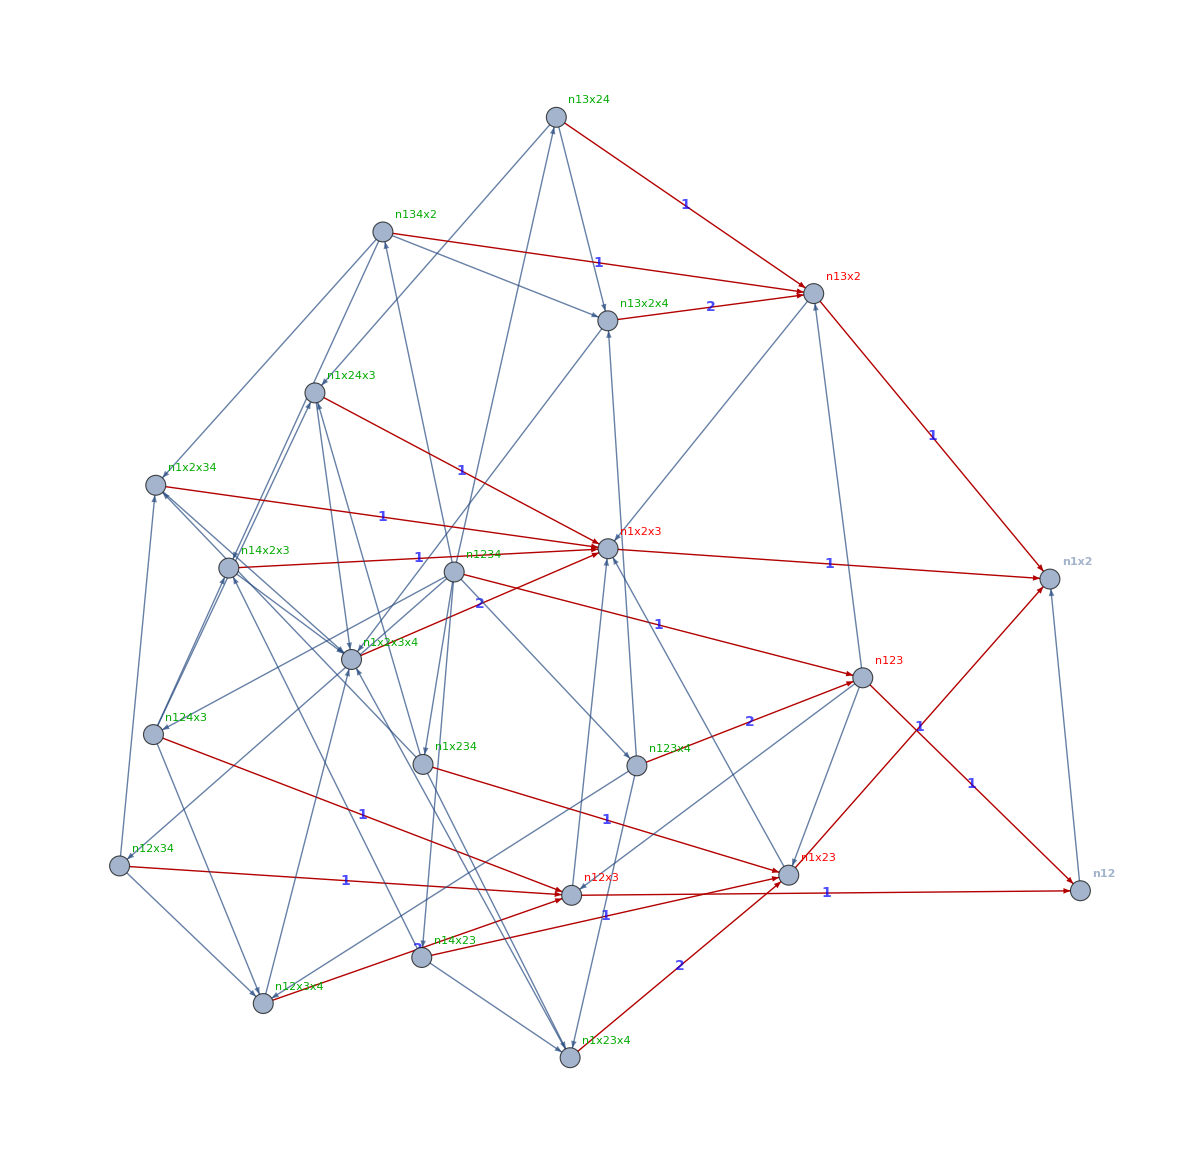

```mathematica
Graph[With[{g=MobiusGraph3[K4Key,allGraphs4],h=MobiusGraph3[k3Key,allGraphs3],i=MobiusGraph3[k2Key,allGraphs2]},
Graph[Join[VertexList[g],VertexList[h],VertexList[i]],Join[joins3,joins2,EdgeList[g],EdgeList[h],EdgeList[i]]]],
GraphHighlight->Join[joins2,joins3],
VertexLabels->
Join[
Table[allGraphs4[k,"colofourrealnull"]->Style[allGraphs4[k,"colofourrealnull"],Darker[Green]],{k,allGraphs5NullAtomKeys}],
Table[allGraphs3[k,"colofourrealnull"]->Style[allGraphs3[k,"colofourrealnull"],Red],{k,allGraphs3NullAtomKeys}],
Table[allGraphs2[k,"colofourrealnull"]->Style[allGraphs2[k,"colofourrealnull"],Bold],{k,allGraphs2NullAtomKeys}]
],
EdgeLabels->Join[joinsLabels,joins3Labels],
GraphLayout->"SpringElectricalEmbedding",
ImageSize->1200]
```